```mathematica
g[fi_] = f*s*Cos[fi]-a
```

-a+f s Cos[fi]

```mathematica
f=300;a=1800;s=18;
```

```mathematica
g[fi]
```

-1800+5400 Cos[fi]

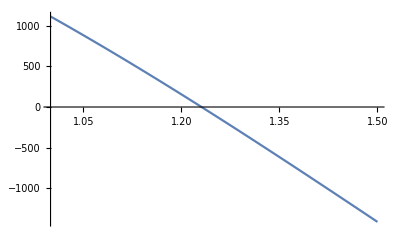

```mathematica
Plot[g[fi],{fi,1,1.5}]
```

```mathematica
g[1]*g[1.5]<0
```

True

```mathematica
prvi[fi_]=D[g[fi],fi]
```

-5400 Sin[fi]

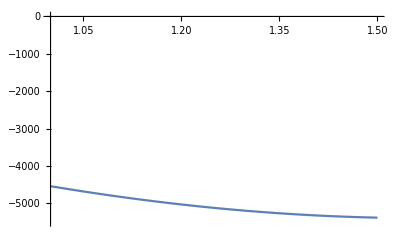

```mathematica
Plot[prvi[fi],{fi,1,1.5},{PlotRange->{-5500,0}}]
```

```mathematica
(*g'(fi)!=0, za sve xϵ[1,1.5]*)
drugi[fi_]=D[g[fi],{fi,2}]
```

-5400 Cos[fi]

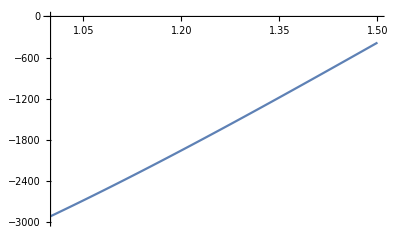

```mathematica
Plot[drugi[fi],{fi,1,1.5},{PlotRange->{-3000,0}}]
```

```mathematica
g[1.5]*drugi[1.5]>0
```

True

```mathematica
g[1]*drugi[1]<0
```

True

```mathematica
iter[0]=1.5
```

1.5

```mathematica
iter[1]=1//N
```

1.

```mathematica
k=1;
```

```mathematica
While[Abs[iter[k]-iter[k-1]]>10^-6,
iter[k+1]=iter[k]-(iter[k]-iter[k-1])/(g[iter[k]]-g[iter[k-1]])g[iter[k]];
k=k+1;
]
Table[iter[i],{i,1,k}]
```

{1.,1.22038,1.23152,1.23096,1.23096,1.23096}

```mathematica
(*drugi*)
res = DSolve[{y[0]==1,y'[t]+2y[t]==E^(2t)+8}, y[t],t]
```

{{y[t]→1/4 ⅇ^(-2 t) (-13+16 ⅇ^(2 t)+ⅇ^(4 t))}}

```mathematica
tacno[t_]=y[t]/.res[[1,1]]
```

1/4 ⅇ^(-2 t) (-13+16 ⅇ^(2 t)+ⅇ^(4 t))

```mathematica
prib={{0,1}}
```

{{0,1}}

```mathematica
h=(1-0)/10//N
```

0.1

```mathematica
f[t_,y_]=-2y+E^(2t)+8;
```

```mathematica
Do[
new = prib[[i,2]]+h*f[prib[[i,1]],prib[[i,2]]];
prib = Append[prib,{prib[[i,1]]+h,new}],
{i,1,10}]
```

```mathematica
prib
```

{{0,1},{0.1,1.7},{0.2,2.28214},{0.3,2.77489},{0.4,3.20213},{0.5,3.58426},{0.6,3.93923},{0.7,4.2834},{0.8,4.63224},{0.9,5.00109},{1.,5.40584}}

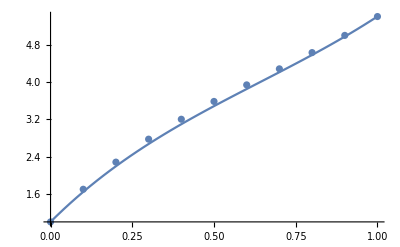

```mathematica
Show[Plot[tacno[t],{t,0,1}],ListPlot[prib]]
```

```mathematica
(*treci*)
po[f_,t_,y_,a_,b_,y0_,n_]:=Module[{},
h=(b-a)/n//N;
ttac[0]=0;
wit[0]=y0;
Do[
ttac[i+1]=ttac[i]+h;
wpom=wit[i]+h/2*f/.{t->ttac[i],y->wit[i]};
wit[i+1]=wit[i]+h*f/.{t->ttac[i]+h/2,y->wpom},
{i,0,n-1}];
Table[{ttac[i],wit[i]},{i,0,n}]
];
```

```mathematica
f[t_,y_]=-2y+E^(2t)+8;
```

```mathematica
prib=po[f[t,y],t,y,0,1,1,10]
```

{{0,1},{0.1,1.64052},{0.2,2.188},{0.3,2.66411},{0.4,3.08772},{0.5,3.47564},{0.6,3.84326},{0.7,4.2052},{0.8,4.57588},{0.9,4.97009},{1.,5.40356}}